# 4-wave interaction amplitude evolutions

Evolves the systems of coupled oscillators for QNMs in the near horizon geometry of RN with asymptotically small but finite Hawking temperature. This is the poincare patch  “κ-AdS2” with a constant electric field (NHERN)

## Importing data

```mathematica
Import["/Users/antares/Library/CloudStorage/Dropbox/Physics projects/Collaborations/4-waves RN/Mathematica NB/RN_ZDMs_4modeCoeffs_Neq1_coeffs_numeric.m"]
```

```mathematica
Length@precomputedS1b234
```

1048576

```mathematica
Import["/Users/antares/Library/CloudStorage/Dropbox/Physics projects/Collaborations/4-waves RN/Mathematica NB/QNM_4mode_data_Neq9_Leq0.m"]
```

4.89238×10^-19-3.73898×10^-18 ⅈ

```mathematica
Clear@softner
```

## Basic Definitions

```mathematica
$Assumptions={x>0,q^2<1/4 ,h>1/2,σ>0, q ∈Reals}; (* assumes ell=0*)
(* set some parameters for supplementary mode *)
λtest = {λ1->{2,3,2},λ2->{3,12,-12},λ3->{2,3,2},λ4->{4,4,1}};
λ0test={λ1->{2,0,0},λ2->{3,0,0},λ3->{2,0,0},λ4->{4,0,0}};
λLMtest={λ1->{0,3,2},λ2->{0,12,-12},λ3->{2,3,2},λ4->{0,4,1}};

 (* number of modes *)
NN=9;
LL = 6;
λ=1;
αval=1;
params={q->1/50,h->1/2+√(1/4-(rp*q)^2),rp->1};
bkgdParams={q-> 2/100,rp->1};  (* supplementary mode paramaters for which q^2<1/4 and L=0 *)
paramsLeq0={q-> 2/100,h->1/2+Sqrt[1/4-(rp*q)^2],rp->1}; 
paramsL[L_Integer]:={q->(q/.bkgdParams),h->1/2+Sqrt[1/4+L*(L+1)-(rp*q)^2],rp->1}
```

```mathematica
(* Basic definitions and operations *)
star[f_]:=Assuming[{h>1/2,q>0}, Conjugate[f]]
bar[f_]:=Assuming[{h>1/2,q>0}, Conjugate[f]]
Γ[x_]:= Gamma[x]
wj[{a_,b_,c_},{d_,e_,f_}] := ThreeJSymbol[{a,d},{b,e},{c,f}]
```

Quasinormal Modes

```mathematica
(* quasinormal mode freq s := -ⅈ*ω *)
sN00[n_Integer]:= -(h+n+ⅈ q)/2  (* supplementary modes L=0 *)
spN00[n_Integer]:=-(1-h+n+ⅈ q)/2  (* principal modes L=0 *)
sNLM[λ_List]:=Block[{h=1/2+Sqrt[1/4+λ[[2]]*(λ[[2]]+1)-q^2]},-(h+λ[[1]] +ⅈ q)/2]
sNLMh[n_,h_]:=-(h+n +ⅈ q)/2

sNLMp[λ_List]:=Block[{h=1/2+Sqrt[1/4+λ[[2]]*(λ[[2]]+1)-q^2]},-(1-h+λ[[1]] +ⅈ q)/2]

ωN00[n_Integer]:= -ⅈ(h+n+ⅈ q)/2  (* supplementary modes *)
ωN00p[Integer_]:=-ⅈ(1-h+n+ⅈ q)/2  (* principal modes *)
ωNLM[λ_List]:=Block[{h=1/2+Sqrt[1/4+λ[[2]]*(λ[[2]]+1)-q^2]},-ⅈ(h+λ[[1]] +ⅈ q)/2]

ωNLMp[λ_List]:=Block[{h=1/2+Sqrt[1/4+λ[[2]]*(λ[[2]]+1)-q^2]},-ⅈ(1-h+λ[[1]] +ⅈ q)/2]

softner[α_Real,t_,n_Integer]:= Exp[sN00[n]* t*α]
softner[α_Real,t_,λ_List]:= Exp[sNLM[λ]* t*α]
```

```mathematica
(* norm of a ell=0 overtone mode *)
 AnormN00[n_]:= Sqrt[(I (-1)^(h+ⅈ q))/Gamma[h-I q] rp^2 (2n!Gamma[2h+n]Gamma[-h-(n-1)- I q])/(Gamma[h+I q +n]/Gamma[h+I q]) ] 
(* norm of an LM overtone *)
 AnormNLM[λ_]:=Block[{h=1/2+Sqrt[1/4+λ[[2]](λ[[2]]+1)-q^2],n=λ[[1]]},
 Sqrt[(I (-1)^(h+ⅈ q))/Gamma[h-I q] rp^2 (2n!Gamma[2h+n]Gamma[-h-(n-1)- I q])/(Gamma[h+I q +n]/Gamma[h+I q]) ] ]
```

```mathematica
hatA[λ_List]:= (A[λ][t])/AnormNLM[λ]
hatAN00[n_integer]:= (A[n][t])/AnormN00[n]
```

### Initial Data and System

```mathematica
genvarst[Nmax_,Lmax_]:=Module[{data},data=Flatten[Table[A[{n,l,m}][t],{n,0,Nmax},{l,0,Lmax},{m,-l,l}],2 (*Flatten to two levels:{n,l,m}*)];
data]
genvarsSphSym[num_]:=Table[A[n],{n,0,num-1}]
```

#### random initial data

```mathematica
genZeroOvertoneInitialData[Lmax_,pow_,sort_:Sort]:=Module[{data,randomValues},(*Generate the list of variables for n=0*)
data=Flatten[Table[A[{0,l,m}][0],{l,0,Lmax},{m,-l,l}],1 ]; (*Flatten one level to create a single list*)
(* Assign random values in the range[1*10^-pow,9*10^-pow] and sort *)
randomValues=Thread[data==sort@RandomReal[{1*10^-pow,9*10^-pow},Length[data]]];
(*Return the list of initial conditions*)randomValues]

genvars[Nmax_,Lmax_]:=Module[{data},data=Flatten[Table[A[{n,l,m}][0],{n,0,Nmax},{l,0,Lmax},{m,-l,l}],2 (*Flatten to two levels:{n,l,m}*)];
data]

genInitialData[Nmax_,Lmax_,pow_]:=Module[{data,randomValues},data=genvars[Nmax,Lmax];(*Generate the list of variables*)randomValues=Thread[data==RandomReal[{1*10^-pow,9*10^-pow},Length[data]]];
randomValues]

setInitsLeq0[ls_,num_]:=Module[
{x=Table[Table[X[0]==i,{i,ls}],{X,genvarsSphSym[num]}]},
Table[x[[i]][[i]],{i,Length[x]}]]

setInitsNeq0[ls_,numL_,pow_]:=Module[
{x=Table[Table[X[0]==i,{i,ls}],{X,genZeroOvertoneInitialData[numL,pow]}]},
Table[x[[i]][[i]],{i,Length[x]}]]
```

#### General {n,l,m} resonant system

```mathematica
GenEqsNLMs[{αN_,αL_,αM_},Nmax_,Lmax_]:= (A[{αN,αL,αM}]'[t])/AnormNLM[{αN,αL,αM}]==sNLM[{αN,αL,αM}](A[{αN,αL,αM}][t])/AnormNLM[{αN,αL,αM}]+ⅈ λ Sum[Sum[Sum[precomputedQ12b3b4[{{γL,γM},{δL,δM},{βL,βM},{αL,αM}}]*precomputedS1b234[{{αN,αL,αM},{βN,βL,βM},{γN,γL,γM},{δN,δL,δM}}] 
(bar[  (A[{βN,βL,βL}][t])/AnormNLM[{βN,βL,βM}]  ])*((A[{γN,γL,γM}][t])/AnormNLM[{δN,γL,γM}])*((A[{δN,δL,δM}][t])/AnormNLM[{δN,δL,δM}]),
{βN,0,Nmax},{βL,0,Lmax},{βM,-βL,βL}],
{γN,0,Nmax},{γL,0,Lmax},{γM,-γL,γL}],
{δN,0,Nmax},{δL,0,Lmax},{δM,-δL,δL} ]

GenEqsNLMω1[{αN_,αL_,αM_},Nmax_Integer,Lmax_Integer]:= (A[{αN,αL,αM}]'[t])/AnormNLM[{αN,αL,αM}]==- ⅈ ωNLM[{αN,αL,αM}](A[{αN,αL,αM}][t])/AnormNLM[{αN,αL,αM}]+ⅈ λ Sum[Sum[Sum[precomputedQ12b3b4[{{γL,γM},{δL,δM},{βL,βM},{αL,αM}}]*precomputedS1b234[{{αN,αL,αM},{βN,βL,βM},{γN,γL,γM},{δN,δL,δM}}] 
(bar[  (A[{βN,βL,βL}][t])/AnormNLM[{βN,βL,βM}]  ])*((A[{γN,γL,γM}][t])/AnormNLM[{δN,γL,γM}])*((A[{δN,δL,δM}][t])/AnormNLM[{δN,δL,δM}]),
{βN,0,Nmax},{βL,0,Lmax},{βM,-βL,βL}],
{γN,0,Nmax},{γL,0,Lmax},{γM,-γL,γL}],
{δN,0,Nmax},{δL,0,Lmax},{δM,-δL,δL} ]

GenEqsNLMω2[{αN_,αL_,αM_},βNmax_,βLmax_,γNmax_,γLmax_,δNmax_,δLmax_]:=ⅈ A[{αN,αL,αM}]'[t]==
Sum[Sum[Sum[
precomputedQ12b3b4[ {{γL,γM},{δL,δM},{βL,βM},{αL,αM}} ]

precomputedS1b234[{{αN,αL,αM},{βN,βL,βM},{γN,γL,γM},{δN,δL,δM}}] 

Exp[ⅈ(ωNLM[{αN,αL,αM}]+ωNLM[{βN,βL,βM}]-ωNLM[{γN,γL,γM}]-ωNLM[{δN,δL,δM}])*t]

bar[A[{βN,βL,βM}][t]] A[{γN,γL,γM}][t] A[{δN,δL,δM}][t] ,
{βN,0,βNmax},{βL,0,βLmax},{βM,-βL,βL}],
{γN,0,γNmax},{γL,0,γLmax},{γM,-γL,γL}],
{δN,0,δNmax},{δL,0,δLmax},{δM,-δL,δL} ]

GenEqsNLMω3[{αN_,αL_,αM_},Nmax_Integer,Lmax_Integer]:=ⅈ A[{αN,αL,αM}]'[t]==
Sum[Sum[Sum[
precomputedQ12b3b4[ {{γL,γM},{δL,δM},{βL,βM},{αL,αM}} ]

precomputedS1b234[{{αN,αL,αM},{βN,βL,βM},{γN,γL,γM},{δN,δL,δM}}] 

Exp[ⅈ(ωNLM[{αN,αL,αM}]+ωNLM[{βN,βL,βM}]-ωNLM[{γN,γL,γM}]-ωNLM[{δN,δL,δM}])*t]

bar[A[{βN,βL,βM}][t]] A[{γN,γL,γM}][t] A[{δN,δL,δM}][t] ,
{βN,0,Nmax},{βL,0,Lmax},{βM,-βL,βL}],
{γN,0,Nmax},{γL,0,Lmax},{γM,-γL,γL}],
{δN,0,Nmax},{δL,0,Lmax},{δM,-δL,δL} ]
```

#### Spherically symmetric (s-wave) resonant system

```mathematica
eqs0=Table[D[hatAN00[n],t]==sN00[n]hatAN00[n]+ⅈ λ/(4π)Sum[S[n,p,q,r] bar[hatAN00[p]]hatAN00[q]hatAN00[r],{p,0,NN-1},{q,0,NN-1},{r,0,NN-1} ],{n,0,NN-1}];
```

```mathematica
eqs1=Table[A[n]'[t]/AnormN00[n]==sN00[n]A[n][t]/AnormN00[n]+ⅈ λ/(4π)Sum[S[n,p,q,r](bar[A[p][t]]A[q][t]A[r][t])/(bar[AnormN00[p]]AnormN00[q] AnormN00[r]),{p,0,NN-1},{q,0,NN-1},{r,0,NN-1} ],{n,0,NN-1}]; 
(* absorbing the fast time frequency *)
eqs2 = Table[A[n]'[t]/AnormN00[n]==-ⅈ λ/(4π)Sum[ S[n,p,q,r]*(bar[A[p][t]]A[q][t]A[r][t])/(bar[AnormN00[p]]AnormN00[q] AnormN00[r]) Exp[(sN00[q]+bar[sN00[p]]+sN00[r]-sN00[n] )t],{p,0,NN-1},{q,0,NN-1},{r,0,NN-1} ],{n,0,NN-1}];
```

```mathematica
swaveEqns[[1]]
```

#### ∑n_i = 0 (zero overtone) resonant system

```mathematica
GenEqs0LM[{αL_,αM_},βLmax_,γLmax_,δLmax_]:= A[{0,αL,αM}]'[t]/AnormNLM[{0,αL,αM}]==- ⅈ ωNLM[{0,αL,αM}](A[{0,αL,αM}][t])/AnormNLM[{0,αL,αM}]+ ⅈ λ Sum[Sum[Sum[precomputedQ12b3b4[{{γL,γM},{δL,δM},{βL,βM},{αL,αM}}]*precomputedS1b234[{{0,αL,αM},{0,βL,βM},{0,γL,γM},{0,δL,δM}}] 
(bar[ A[{0,βL,βL}][t]/AnormNLM[{0,βL,βM}]])
(A[{0,γL,γM}][t]/AnormNLM[{0,γL,γM}])
(A[{0,δL,δM}][t]/AnormNLM[{0,δL,δM}]),
{βL,0,βLmax},{βM,-βL,βL}],
{γL,0,γLmax},{γM,-γL,γL}],
{δL,0,δLmax},{δM,-δL,δL}]
```

```mathematica
GenerateEqs0LMSystem[Lmax_,βLmax_,γLmax_,δLmax_]:=
Module[{eqs},eqs=Flatten[Table[GenEqs0LM[{l,m},βLmax,γLmax,δLmax],{l,0,Lmax},{m,-l,l}]];
eqs]
GenerateEqsNLMSystem[{αNmax_,αLmax_},Nmax_,Lmax_]:=Module[{eqs},eqs=Flatten[Table[GenEqsNLMs[{n,l,m},Nmax,Lmax],{n,0,αNmax},{l,0,αLmax},{m,-l,l}]];
eqs]
```

```mathematica
(*evolEqnsnEq0[{αL_,αM_},βLmax_,γLmax_,δLmax_]:= ⅈ A[{0,αL,αM}]'[t]/AnormLM[{0,αL,αM}] == Sum[Sum[Sum[
precomputedQLM[{{γL,γM},{δL,δM}},{βL,βM},{αL,αM} ]

SLM[{0,αL,αM},{0,βL,βM},{0,γL,γM},{0,δL,δM}] 

Exp[ⅈ(ωLM[{0,αL,αM}]+ωLM[{0,βL,βM}]-ωLM[{0,γL,γM}]-ωLM[{0,δL,δM}])*t]

bar[A[{0,βL,βM}][t]/AnormLM[{0,βL,βM}]] (A[{0,γL,γM}][t]/AnormLM[{0,γL,γM}]) (A[{0,δL,δM}][t]/AnormLM[{0,δL,δM}]) ,
{βL,0,βLmax},{βM,-βL,βL}],
{γL,0,γLmax},{γM,-γL,γL}],
{δL,0,δLmax},{δM,-δL,δL}] *)
```

### Solution generation and plotting

```mathematica
(* solve the system of equations *)
genSols[params_,tmax_,eqnSys_,initaldataset_,vars_]:=NDSolve[
Join[
eqnSys//.params//Simplify, initaldataset
],
vars,{t,0, tmax}]

genSolsLeq0Sorted[numModes_,eqs_,pow_,params_,tmax_]:=NDSolve[
Join[
eqs//.params//Simplify,setInitsLeq0[RandomReal[{ 1 10^-pow,9 10^-pow},numModes],numModes]
],
genvarsSphSym[numModes],{t,0, tmax}]

genSolsLeq0Sorted[numModes_,eqs_,pow_,params_,tmax_]:=NDSolve[
Join[
eqs//.params//Simplify,setInitsLeq0[Sort[RandomReal[{ 1 10^-pow,9 10^-pow},numModes]],numModes]
],
genvarsSphSym[numModes],{t,0, tmax}]

genSolsLeq0RevSorted[numModes_,eqs_,pow_,params_,tmax_]:=NDSolve[
Join[
eqs//.params//Simplify,setInitsLeq0[ReverseSort[RandomReal[{ 1 10^-pow,9 10^-pow},numModes]],numModes]
],
genvarsSphSym[numModes],{t,0, tmax}]
genInterpsWithSoftener[Nmax_,Lmax_,α_,sols_]:=Flatten[Table[(A[{n,l,m}][t]/.sols)*softner[α,t,{n,l,m}]/.bkgdParams,{n,0,Nmax},{l,0,Lmax},{m,-l,l}],2 ]
```

```mathematica
GetColors1[n_]:=Module[{palette=ColorData[97,"ColorList"]},Table[palette[[Mod[i-1,Length[palette]]+1]],{i,n}]]
GetColors2[n_]:=ColorData["Rainbow"]/@Rescale[Range[n]];
GenLegend[alist_List]:=Module[{labels,colors,n=Length[alist]},
labels=Table[Module[{p,l,m},{p,l,m}=First@Head@alist[[i]];
"n="<>ToString[p]<>", l="<>ToString[l]<>", m="<>ToString[m]],{i,n}];
colors=GetColors1[n];(*use either method above*)Placed[LineLegend[colors,labels],Right]]

GenLegendWithColors[alist_List]:=Module[{labels,colors,n=Length[alist]},labels=Table[Module[{n,l,m},{n,l,m}=First@Head@alist[[i]];
"n="<>ToString[n]<>", l="<>ToString[l]<>", m="<>ToString[m]],{i,n}];
colors=GetColors2[n];
{colors,Placed[LineLegend[colors,labels],Right]}]
```

## Coupled Mode System Evolutions

### General Evolutions

```mathematica
EqsNmaxEq1LmaxEq2=GenerateEqsNLMSystem[{1,2},1,2];
```

```mathematica
dataNmaxEq1LmaxEq2 = genInitialData[1,2,7];
```

```mathematica
%
```

{A[{0,0,0}][0]==6.60816×10^-7,A[{0,1,-1}][0]==7.60152×10^-7,A[{0,1,0}][0]==1.59744×10^-7,A[{0,1,1}][0]==6.45807×10^-7,A[{0,2,-2}][0]==8.76304×10^-7,A[{0,2,-1}][0]==3.78893×10^-7,A[{0,2,0}][0]==8.51695×10^-7,A[{0,2,1}][0]==8.6954×10^-7,A[{0,2,2}][0]==6.95365×10^-7,A[{1,0,0}][0]==1.24512×10^-7,A[{1,1,-1}][0]==6.78781×10^-7,A[{1,1,0}][0]==8.27923×10^-7,A[{1,1,1}][0]==4.88543×10^-7,A[{1,2,-2}][0]==7.88768×10^-7,A[{1,2,-1}][0]==2.54411×10^-7,A[{1,2,0}][0]==8.91217×10^-7,A[{1,2,1}][0]==4.647×10^-7,A[{1,2,2}][0]==2.79398×10^-7}

```mathematica
solsNmaxEq1LmaxEq2 = genSols[bkgdParams, 10, EqsNmaxEq1LmaxEq2, dataNmaxEq1LmaxEq2,genvarst[1,2]]
```

{{A[{0,0,0}][t]→InterpolatingFunction[…][t],A[{0,1,-1}][t]→InterpolatingFunction[…][t],A[{0,1,0}][t]→InterpolatingFunction[…][t],A[{0,1,1}][t]→InterpolatingFunction[…][t],A[{0,2,-2}][t]→InterpolatingFunction[…][t],A[{0,2,-1}][t]→InterpolatingFunction[…][t],A[{0,2,0}][t]→InterpolatingFunction[…][t],A[{0,2,1}][t]→InterpolatingFunction[…][t],A[{0,2,2}][t]→InterpolatingFunction[…][t],A[{1,0,0}][t]→InterpolatingFunction[…][t],A[{1,1,-1}][t]→InterpolatingFunction[…][t],A[{1,1,0}][t]→InterpolatingFunction[…][t],A[{1,1,1}][t]→InterpolatingFunction[…][t],A[{1,2,-2}][t]→InterpolatingFunction[…][t],A[{1,2,-1}][t]→InterpolatingFunction[…][t],A[{1,2,0}][t]→InterpolatingFunction[…][t],A[{1,2,1}][t]→InterpolatingFunction[…][t],A[{1,2,2}][t]→InterpolatingFunction[…][t]}}

```mathematica
{colors,legend}=GenLegendWithColors[genvarst[1,2]];
```

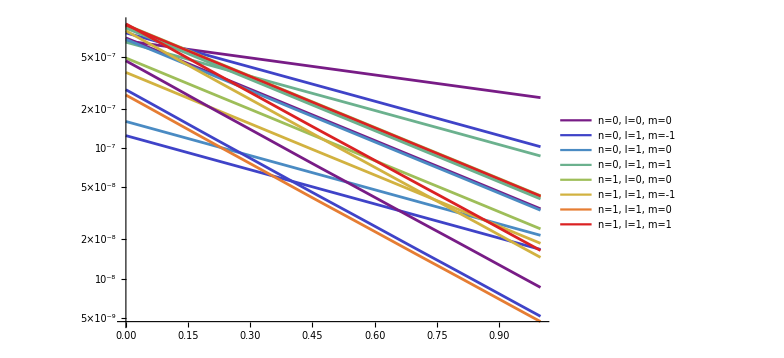

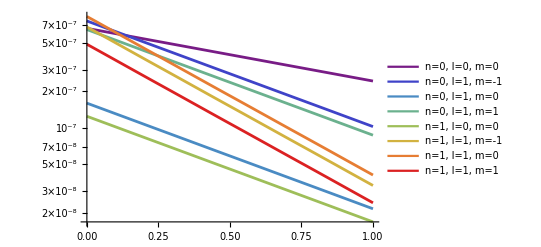

-Graphics-

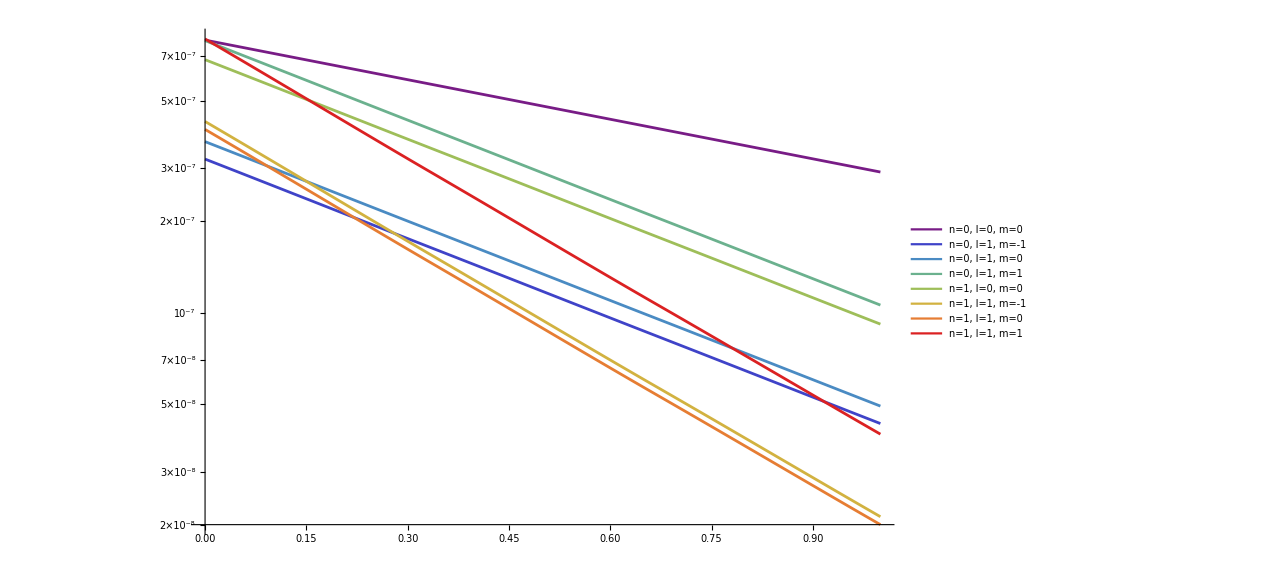

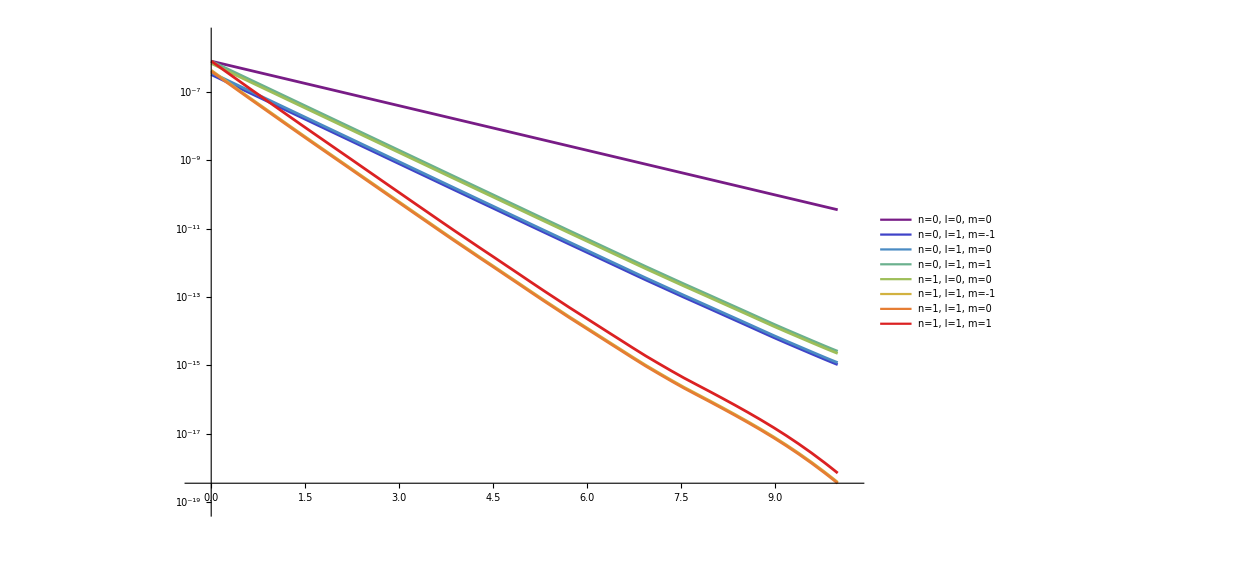

```mathematica
plot=With[{curves=Abs[genInterpsWithSoftener[1,2,1.0,solsNmaxEq1LmaxEq2]]},LogPlot[curves,{t,0,1},PlotStyle->colors,PlotLegends->legend]]
```

### ∑n_j = 0 (zero overtone) evolutions

```mathematica
testSys=GenerateEqs0LMSystem[3,3,3,3];
testData = genZeroOvertoneInitialData[3,7];
```

```mathematica
testSols = genSols[bkgdParams, 10, testSys, testData,genvarst[0,3]];
```

```mathematica
{colors,legend}=GenLegendWithColors[genvarst[0,3]];
```

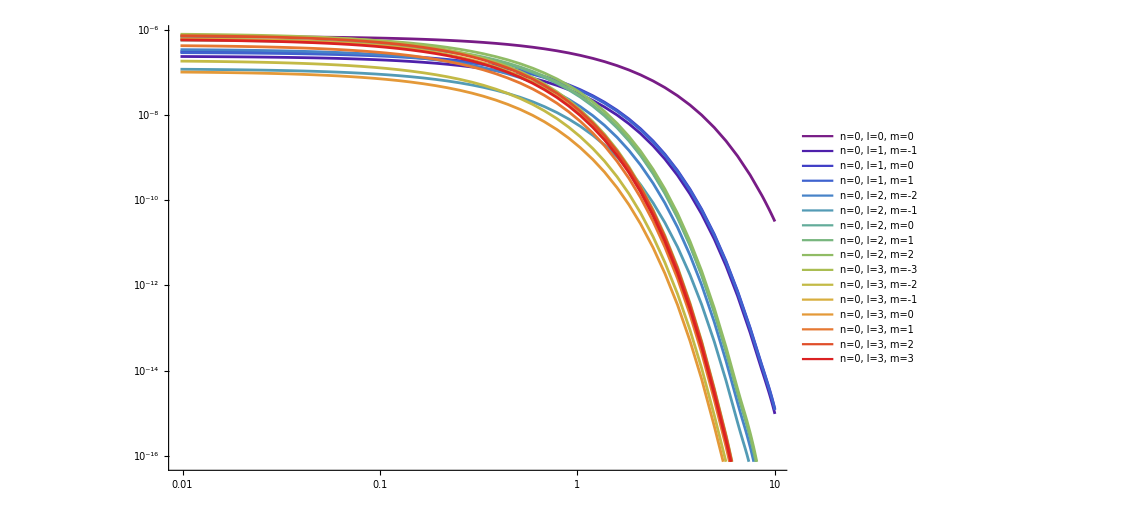

```mathematica
With[{curves=Abs[genInterpsWithSoftener[0,3,1.0,testSols]]},LogLogPlot[curves,{t,0,10},PlotStyle->colors,PlotLegends->legend]]
```

### ell = 0 simulations

```mathematica
GenLegendLeq0[vars_List]:=Module[{labels,colors,n=Length[vars]},
labels=Table["n="<>ToString[i],{i,n}];
colors=GetColors1[n];
Placed[LineLegend[colors,labels],Right]]

plotSysLeq0[system_,tmin_,tmax_,func_,α_:1]:=LogPlot[Evaluate[Table[{func[A[num][t]softner[α,t,num]]}//.params/.system,{num,0,NN-1}]],{t,0,tmax},PlotRange->All,PlotLegends->GenLegendLeq0[genvarsSphSym[NN]]]
```

```mathematica
Length@swaveEqns
```

9

```mathematica
NN
```

9

```mathematica
eqs1//Length
```

8

```mathematica
solLeq0Rand[1]=genSols[params, 1, swaveEqns,setInitsLeq0[RandomReal[{ 1 10^-7,9 10^-7},NN],NN],genvarsSphSym[NN]];
```

NDSolve::ndsz: At t == 0.247629, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solLeq0Rand[1]=genSols[params, 1, swaveEqns,setInitsLeq0[RandomReal[{ 1 10^-7,9 10^-7},NN],NN],genvarsSphSym[NN]];
solLeq0Rand[2]=genSols[ params, 10, swaveEqns,setInitsLeq0[RandomReal[{ 1 10^-10,9 10^-10},NN],NN],genvarsSphSym[NN]];
solLeq0Rand[3]=genSols[ params, 100, swaveEqns,setInitsLeq0[RandomReal[{ 1 10^-12,9 10^-12},NN],NN],genvarsSphSym[NN]];
solLeq0Rand[4]=genSols[ params, 500, swaveEqns,setInitsLeq0[RandomReal[{ 1 10^-15,9 10^-15},NN],NN],genvarsSphSym[NN]];
```

```mathematica
solLeq0Rand[3]
```

{{A[0]→InterpolatingFunction[…],A[1]→InterpolatingFunction[…],A[2]→InterpolatingFunction[…],A[3]→InterpolatingFunction[…],A[4]→InterpolatingFunction[…],A[5]→InterpolatingFunction[…],A[6]→InterpolatingFunction[…],A[7]→InterpolatingFunction[…],A[8]→InterpolatingFunction[…]}}

```mathematica
solLeq0Direct[1]=genSolsLeq0Sorted[NN,swaveEqns,7,params,1];
solLeq0Direct[2]=genSolsLeq0Sorted[NN,swaveEqns, 10,params,10];
solLeq0Direct[3]=genSolsLeq0Sorted[NN,swaveEqns, 12,params,20];
solLeq0Direct[4]=genSolsLeq0Sorted[NN,swaveEqns,15, params,50];
```

```mathematica
solLeq0Inv[1]=genSolsLeq0RevSorted[NN,swaveEqns, 7,params,1];
solLeq0Inv[2]=genSolsLeq0RevSorted[NN,swaveEqns,10,params,10];
solLeq0Inv[3]=genSolsLeq0RevSorted[NN,swaveEqns,12,params,20];
solLeq0Inv[4]=genSolsLeq0RevSorted[NN,swaveEqns,15, params,50];
```

```mathematica
(*{A[0][0]==6.271649333813016*^-7,A[1][0]==6.977536648130945*^-7,A[2][0]==5.301843484425725*^-7, A[3][0]==3.1524290501834394*^-7,A[4][0]==6.047258929143997*^-7,A[5][0]==3.8104659619505917*^-7,A[6][0]==5.37026645211329*^-7,A[7][0]==8.233916836522037*^-7,A[8][0]==4.3127851154016284*^-7}*)
```

```mathematica
(*Save["system_solns_Neq9",solsys] *)
```

```mathematica
plotSysLeq0[solLeq0Rand[1][[1]],0,.001,Abs,0]
plotSysLeq0[solLeq0Rand[2][[1]],0,1,Abs,0]
plotSysLeq0[solLeq0Rand[3][[1]],0,10,Abs,0]
plotSysLeq0[solLeq0Rand[4][[1]],0,100,Abs,0]
```

-Graphics-

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

ReplaceAll::reps: {Divide[(A[0])'[t], Power[2, <<1>>] Power[Divide[I <<3>> Gamma[1 + <<2>>], <<1>>], <<1>>]] == <<1>>, <<15>>} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

ReplaceAll::reps: {Divide[(A[0])'[t], Power[2, <<1>>] Power[Divide[I <<3>> Gamma[1 + <<2>>], <<1>>], <<1>>]] == <<1>>, <<15>>} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

$Aborted

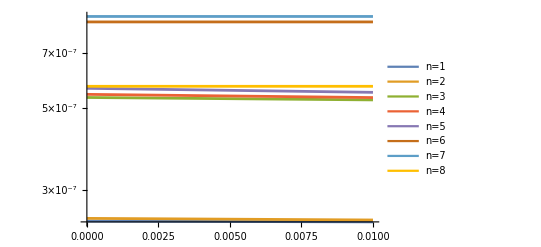

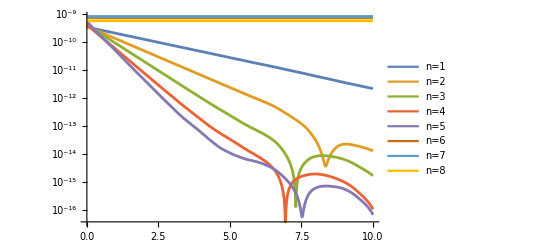

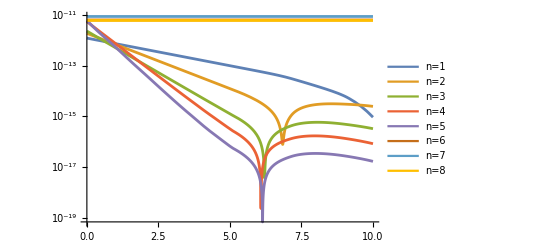

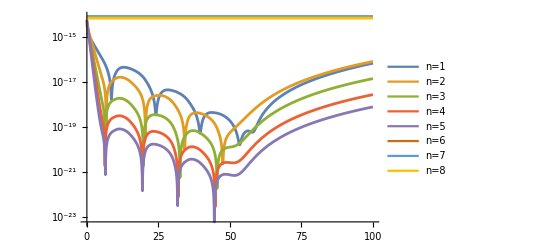

```mathematica
plotSysLeq0[solLeq0Direct[1][[1]],0,.01,Abs,0]
plotSysLeq0[solLeq0Direct[2][[1]],0,10,Abs,0]
plotSysLeq0[solLeq0Direct[3][[1]],0,10,Abs,0]
plotSysLeq0[solLeq0Direct[4][[1]],0,100,Abs,0]
```

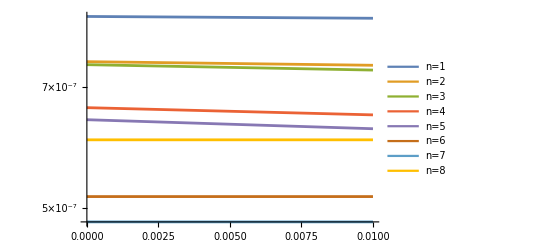

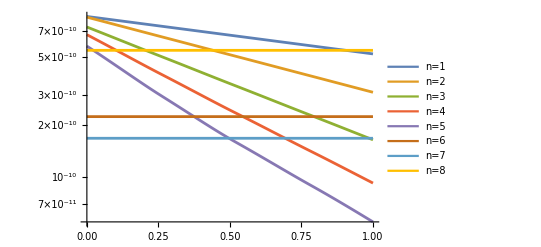

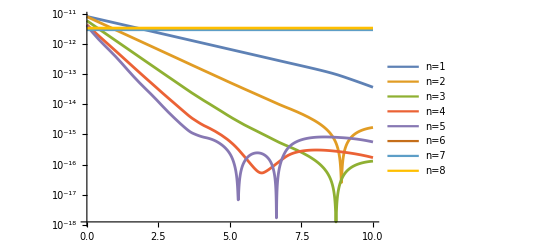

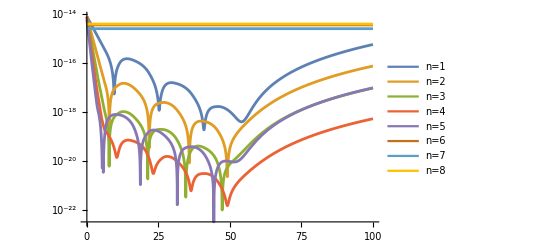

```mathematica
plotSysLeq0[solLeq0Inv[1][[1]],0,.01,Abs,0]
plotSysLeq0[solLeq0Inv[2][[1]],0,1,Abs,0]
plotSysLeq0[solLeq0Inv[3][[1]],0,10,Abs,0]
plotSysLeq0[solLeq0Inv[4][[1]],0,100,Abs,0]
```

```mathematica
(*SetDirectory["/Users/antares/Documents/Physics_Research/My NBs/Near horizon/"];*)
```

```mathematica
(*Save["amplitudes_Neq9",{solDirect,solInverse}] *)
```

$Aborted

```mathematica
PolyGamma[0,1]
```

-EulerGamma

```mathematica
InverseLaplaceTransform[Exp[-π s],s,t]
```

DiracDelta[-π+t]